```mathematica
Clear["Global`*"]
Off[DeleteDirectory::nodir]
(*Required Package*)
Needs["ErrorBarPlots`"]
(*Required Folder*)
SetDirectory[NotebookDirectory[]]
DeleteDirectory["ResultsNonLinear",DeleteContents->True];
CreateDirectory["ResultsNonLinear"];
(*Dataset Folder Path*)
dataPath="/home/edwin/Dropbox/Cinvestav Experiments/Project/Results/down/2*/seq*/reParticula*.dat";
```

/home/edwin/Dropbox/Cinvestav Experiments/Project/Computational/Modules

#### Calibration

```mathematica
(*z Steps in μm*)
zStep=0.5;
(*Px to μm*)
Px=0.127735(*μm*);
(*Carvajal Parameters*)
α1=30.8437/Px(*Px*);
α2=1/145.2783 (*μm^-1*);
α3=-31.0573/Px(*Px*);
```

```mathematica
(*Number of Particles*)
nFile=Length@FileNames[dataPath];
```

```mathematica
(*Import Data*)
data=Table[Import[FileNames[dataPath][[i]],"Data"],{i,nFile}];
```

```mathematica
(*Radius List*)
RListRaw=Table[Last/@data[[i]],{i,nFile}];
RList=Table[
aux=RListRaw[[i]];θ=1;
While[
RListRaw[[i,θ]]==0.,
aux=Drop[aux,1];θ++];
aux,
{i,nFile}];
```

```mathematica
(*Match Dataset Lengths*)
Lengths=Table[Length@RList[[i]],{i,nFile}];
RList=Map[Take[#,Min@Lengths]&,RList];
zList=Range[0.5,Min@Lengths zStep,zStep];
```

```mathematica
(*Calibration*)
zRList=Table[DeleteCases[Transpose[{zList,RList[[i]]}],{_,0.}],{i,nFile}];
```

```mathematica
(*Calibration Fits*)
zRFits=Table[NonlinearModelFit[zRList[[i]],a1 Exp[a2 x]+a3,{{a1,α1},{a2,α2},{a3,α3}},x,Method->"NMinimize"],{i,nFile}];
RMeanList=Mean/@Transpose[Table[Table[zRFits[[j]][zList[[i]]],{i,Length@zList}],{j,nFile}]];
σMeanList=StandardDeviation/@Transpose[Table[Table[zRFits[[j]][zList[[i]]],{i,Length@zList}],{j,nFile}]];
zRMeanList=Transpose[{zList,RMeanList}];
zRFit=NonlinearModelFit[zRMeanList,a1 Exp[a2 x]+a3,{{a1,α1},{a2,α2},{a3,α3}},x,Method->"NMinimize",Weights->1/σMeanList^2];
```

```mathematica
(*Degrees of Freedom*)
ν=zRFit["ANOVATableDegreesOfFreedom"][[2]];
(*Reduced χ^2*)
χ2ν=Total[zRFit["StandardizedResiduals"]^2]/ν;
(*Probability*)
P=SurvivalFunction[ChiSquareDistribution[ν],χ2ν ν];
(*Autocorrelation Test*)
d=Total[Differences[zRFit["StandardizedResiduals"]]^2]/Total[zRFit["StandardizedResiduals"]^2];
```

#### Print Results

Statistical Parameters

R^2 = 1.

ν = 15.

χ_ν^2 = 1.321

P(χ_ν^2;ν) = 0.1793

D = 0.1646

| Estimate | Standard Error | t-Statistic | P-Value
a1 | 493.994 | 28.1079 | 17.5749 | 2.03498×10^-11
a2 | 0.00716772 | 0.000395517 | 18.1224 | 1.30974×10^-11
a3 | -488.144 | 28.1175 | -17.3608 | 2.42586×10^-11

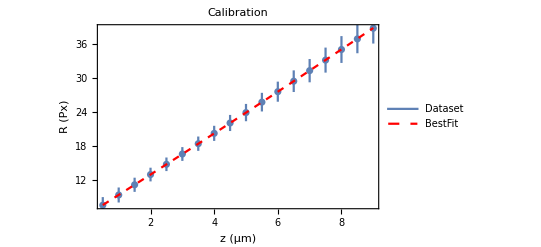

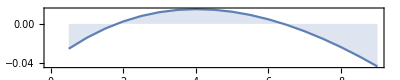

```mathematica
(*Print Results*)
Print[]
Print[Style["Statistical Parameters",Underlined]]
Print["R^2 = ", SetPrecision[zRFit["RSquared"],4]]
Print["ν = ", SetPrecision[ν,4]]
Print["χ_ν^2 = ", SetPrecision[χ2ν,4]]
Print["P(χ_ν^2;ν) = ", SetPrecision[P,4]]
Print["D = ", SetPrecision[d,4]]
Print[zRFit["ParameterTable"]]
Print[]
(*Fit Plot*)
zRMeanListσ=MapAt[ErrorBar,Transpose[{zRMeanList,σMeanList}],{All,2}];
plot=Legended[Show[
ErrorListPlot[zRMeanListσ],
Plot[zRFit[x],{x,First@zList,Last@zList},PlotStyle->{Red,Dashed}],
Frame->True,
FrameLabel->{"z (μm)","R (Px)"},
PlotLabel->"Calibration",
PlotRange->{{Min[First/@zRMeanList],Max[First/@zRMeanList]},{Min@DeleteCases[RMeanList,0.],Max@RMeanList}}],Placed[LineLegend[{ColorData[97][1],{Red,Dashed}},{"Dataset","BestFit"},LegendFunction->Panel],{{0.05,0.7},{0,0}}]]
(*Residuals Plot*)
ResPlot=ListLinePlot[Transpose[{First/@zRMeanList,zRFit["FitResiduals"]}], 
AspectRatio->1/5,
Frame->True,
Filling->Axis,
FrameLabel->{"z (μm)",""},
PlotLabel->"Residuals"]
```

```mathematica
(*Export Numerical Results & Plots*)
Export["ResultsNonLinear/CalibrationPlot.pdf",plot];
Export["ResultsNonLinear/Residuals.pdf",ResPlot];
Export["ResultsNonLinear/R2.dat",SetPrecision[zRFit["RSquared"],4]];Export["ResultsNonLinear/DoF.dat",SetPrecision[ν,4]];Export["ResultsNonLinear/Chi2.dat",SetPrecision[χ2ν,4]];Export["ResultsNonLinear/P.dat",SetPrecision[P,4]];
Export["ResultsNonLinear/D.dat",SetPrecision[d,4]];
Export["ResultsNonLinear/a1.dat",SetPrecision[a1/.zRFit["BestFitParameters"],4]];
Export["ResultsNonLinear/a2.dat",SetPrecision[a2/.zRFit["BestFitParameters"],4]];
Export["ResultsNonLinear/a3.dat",SetPrecision[a3/.zRFit["BestFitParameters"],4]];
```